Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1.  Graph the probability function f[x] = k x^2 (x = 1, 2, 3, 4, 5; k suitable) and the distribution function.

```mathematica
gvn=Table[x^2,{x,1,5}]
```

{1,4,9,16,25}

```mathematica
Total[gvn]
```

55

The suitable k will make an area of 1 for the pdf.

```mathematica
N[1/%]
```

0.0181818

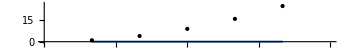

```mathematica
Plot[0.018181818,{x,1,5},Filling->Axis,ImageSize->350,Epilog->{(*{Text[Style["(2, k)",Medium],{1.8,0.2}]},*){Point[{1,1}]},{Point[{2,4}]},{Point[{3,9}]},{Point[{4,16}]},{Point[{5,25}]}},ImagePadding->15,PlotRange->{{0,6},{-1,27}},AspectRatio->0.05]
```

3.  Uniform distribution. Graph f and F when the density of X is f[x] = k = const if -2 ≤ x ≤ 2 and elsewhere. Find P(0 ≤ X ≤ 2).

It is a feature of a uniform distribution that its graph has area 1. So if 0 ≤ x ≤ 2 is half the interval assigned, then the area is 1/2 . At attempt was made to graph f.

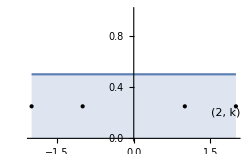

```mathematica
Plot[0.5,{x,-2,2},Filling->Axis,ImageSize->250,Epilog->{{Text[Style["(2, k)",Medium],{1.8,0.2}]},{Point[{-2,0.25}]},{Point[{-1,0.25}]},{Point[{1,0.25}]},{Point[{2,0.25}]}},ImagePadding->15]
```

5.  Graph f and F when f[-2] = f[2] = 1/8, f[-1] = f[1] = 3/8. Can f have further positive values?

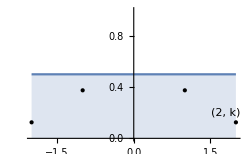

```mathematica
Plot[0.5,{x,-2,2},Filling->Bottom,ImageSize->250,Epilog->{{Text[Style["(2, k)",Medium],{1.8,0.2}]},{Point[{-2,0.125}]},{Point[{-1,0.375}]},{Point[{1,0.375}]},{Point[{2,0.125}]}},ImagePadding->15]
```

7.  Let X be the number of years before a certain kind of pump needs replacement. Let X have the probability function f[x] = k x^3 , x = 0, 1, 2, 3, 4. Find k. Sketch f and F.

Since the f[x] values add to 100, and the area of the distribution function is supposed to be 1 by numbered line (6) on p. 1032, I put the top of the distribution function curve at 0.01.

```mathematica
Sum[x^3,{x,0,4}]
```

100

```mathematica
p1=Plot[0.01,{x,0,4},Filling->{Axis},ImageSize->250,Epilog->{(*{Text[Style["(2, k)",Medium],{1.8,0.2}]},*){Point[{0,0.0}]},{Point[{1,1}]},{Point[{2,8}]},{Point[{3,27}]},{Point[{4,64}]}},ImagePadding->15,PlotRange->{{0,4.1},{0,65}}];
```

```mathematica
p2=Plot[0.01,{x,0,4},Filling->Axis,ImageSize->250,PlotLabel->"Detail",Epilog->{{Point[{0,0.0}]},{Point[{1,1}]},{Point[{2,8}]},{Point[{3,27}]},{Point[{4,64}]}},ImagePadding->30,PlotRange->{{-0.02,4.1},{-0.001,1.1}}];
```

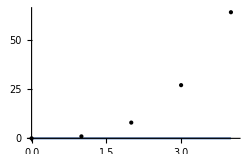
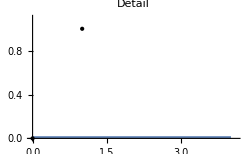

```mathematica
Row[{p1,p2}]
```

9.  Let X (millimeters) be the thickness of washers. Assume that X has the density f[x] = k x if 0.9 < x < 1.1 and 0 otherwise. Find k. What is the probability that a washer will have thickness between 0.95 mm and 1.05 mm?

This does not look uniform anymore, I think I have entered the territory of continuous distributions.

```mathematica
f[x_]=Piecewise[{{0,-∞<x≤0.9},{5 x,0.9<x<1.1},{0,1.1≤x<∞}}]
```

Piecewise[{{0, -∞<x≤0.9}, {5 x, 0.9<x<1.1}, {0, True}}]

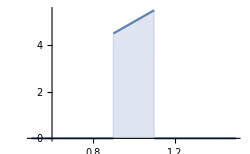

```mathematica
Plot[f[x],{x,0.5,1.5},ImageSize->250,Filling->Bottom]
```

If k is chosen as 5, then numbered line (10) on p. 1033 holds.

```mathematica
Integrate[5 x,{x,0.9,1.1}]
```

1.

For the probability of the washer thickness limits asked for, I do another integral, which as a ratio of areas, equals 50% probability.

```mathematica
Integrate[5 x,{x,0.95,1.05}]
```

0.5

11.  Find the probability that none of three bulbs in a traffic signal will have to be replaced during the first 1500 hours of operation if the lifetime X of a bulb is a random variable with the density f[x] = 6 (0.25 - (x - 1.5)^2) when 1 ≤ x ≤ 2 and f[x] = 0 otherwise, where x is measured in multiples of 1000 hours.

```mathematica
f[x_]=Piecewise[{{0,-∞<x<1},{6 (0.25-(x-1.5)^2),1≤x≤2},{0,2<x<∞}}]
```

Piecewise[{{0, -∞<x<1}, {6 (0.25-(-1.5+x)^2), 1≤x≤2}, {0, True}}]

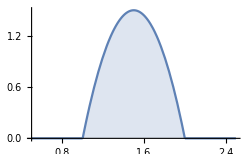

```mathematica
Plot[f[x],{x,0.5,2.5},ImageSize->250,Filling->Bottom]
```

Luckily the bounds chosen in the problem make the probability function integral equal to 1.

```mathematica
Integrate[f[x],{x,1,2}]
```

1.

The area under the curve represents the entire lifetime of a bulb. The probability that it will fail by the halfway point in its expected life is

```mathematica
Integrate[f[x],{x,1,1.5}]
```

0.5

Meaning that the probability that it will not fail is

```mathematica
1-0.5
```

0.5

The probability for not failing is the same with all three bulbs, so the probability that none will fail by 1500 hours service time is

```mathematica
0.5^3
```

0.125

In other words, it looks like an 87.5 percent chance of at least one bulb requiring replacement in that time.

13.  Suppose that in an automatic process of filling oil cans, the content of a can (in gallons) is Y = 100 + X, where X is a random variable with density f[x] = 1 - Abs[x] when Abs[x] ≤ 1 and 0 when Abs[x] > 1. Sketch f[x] and F[x]. In a lot of 1000 cans, about how many will contain 100 gallons or more? What is the probability that a can will contain less than 99.5 gallons? Less than 99 gallons?

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Piecewise[{{1-Abs[x],Abs[x]≤1},{0,Abs[x]>1}}]
```

Piecewise[{{1-Abs[x], Abs[x]≤1}, {0, True}}]

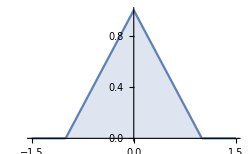

```mathematica
Plot[f[x],{x,-1.5,1.5},ImageSize->250,Filling->Axis]
```

Since Abs is an even function, I can expect

```mathematica
Integrate[1-Abs[x],{x,-1,1}]
```

1

So it appears that the volume will never be below 99 gal. As the PDF is centered on zero, 500 out of 1000 cans will have volume of 100 gal or more. The probability that a can will contain less than 99.5 gal is

```mathematica
Integrate[1-Abs[x],{x,-1,-0.5}]
```

0.125

The probability that it will contain less than 99 gal is zero.

15.  Let X be a random variable that can assume every real value. What are the complements of the events X ≤ b, X < b, X ≥ c, X > c, b ≤ X ≤ c, b < X ≤ c ?

These are the expressions which account for the opposite possibilities, X ≥ b, X < c, X ≤ c, b > X > c, b ≥ X > c.